```mathematica
Quit[]
```

```mathematica
eq1=ⅈ ℏ D[Ψ[t,x],t]==-ℏ^2/(2m)D[Ψ[t,x],{x,2}]+m U[x]Ψ[t,x];
eq2=D[U[x],{x,2}]==4π G m Ψ[t,x]Ψ[t,x];
```

```mathematica
rule={t->((2m)/Λ)^-1 t,Ψ[t,x]->((π G Λ^2)/(2m))^(-1/2)Ψ, D[Ψ[t,x],t]->((π G Λ^2)/(2m))^(-1/2)((2m)/Λ)dtΨ,
       x->((2m)/(Λ^(1/2)ℏ^(1/2)))^-1 x,D[Ψ[t,x],{x,1}]->((π G Λ^2)/(2m))^(-1/2)((2m)/(Λ^(1/2)ℏ^(1/2)))dΨ, D[Ψ[t,x],{x,2}]->((π G Λ^2)/(2m))^(-1/2)((2m)/(Λ^(1/2)ℏ^(1/2)))^2 ddΨ,U[x]->(Λ/(2ℏ))^-1 U, D[U[x],{x,2}]->(Λ/(2ℏ))^-1((2m)/(Λ^(1/2)ℏ^(1/2)))^2 ddU};
```

```mathematica
(*Evaluando*)
```

```mathematica
temp=eq1/.rule//PowerExpand//Simplify;
Solve[temp,dtΨ ]
```

{{dtΨ→(-ddΨ+U Ψ)/i}}

```mathematica
temp=eq2/.rule//Simplify;
Solve[temp,ddU ]
```

{{ddU→Ψ^2}}

```mathematica
(*Funcional de energía*)
eq3={ℏ^2/(2m)D[Ψ[t,x],x]^2 x^3,-(G m^2)/2 Ψ[t,x]^4 x^6/x}/.rule//Simplify
```

{(dΨ^2 x^3 ℏ^(5/2))/(2 G m π Λ^(3/2)),-(x^5 Ψ^4 ℏ^(5/2))/(16 G m π^2 Λ^(3/2))}

```mathematica
(*Taylor*)
```

```mathematica
$Assumptions=En∈Reals;
```

```mathematica
Syst={(En σ[r]-U[r] σ[r])+Laplacian[σ[r],{r,θ,ϕ},"Spherical"]==0,Laplacian[U[r],{r,θ,ϕ},"Spherical"]-σ[r]^2==0};
```

```mathematica
seq1=Series[Syst[[1,1]],{r,0,4}];
seq2=Series[Syst[[2,1]],{r,0,4}];
```

```mathematica
Om1seq1=Coefficient[seq1,r,-1];
O0seq1=Coefficient[seq1,r,0];
O1seq1=Coefficient[seq1,r,1];
O2seq1=Coefficient[seq1,r,2];
O3seq1=Coefficient[seq1,r,3];

Om1seq2=Coefficient[seq2,r,-1];
O0seq2=Coefficient[seq2,r,0];
O1seq2=Coefficient[seq2,r,1];
O2seq2=Coefficient[seq2,r,2];
O3seq2=Coefficient[seq2,r,3];
```

```mathematica
d1=Last@Solve[{Om1seq1==0,Om1seq2==0},{σ'[0],U'[0]}]
d2=Last@Solve[{O0seq1==0,O0seq2==0}/.d1,{σ''[0],U''[0]}]
d3=Last@Solve[{O1seq1==0,O1seq2==0}/.d1/.d2,{σ'''[0],U'''[0]}]
d4=Last@Solve[{O2seq1==0,O2seq2==0}/.d1/.d2/.d3,{σ''''[0],U''''[0]}]
d5=Last@Solve[{O3seq1==0,O3seq2==0}/.d1/.d2/.d3/.d4,{σ'''''[0],U'''''[0]}]
```

{σ'[0]→0,U'[0]→0}

{σ''[0]→1/3 (-En σ[0]+U[0] σ[0]),U''[0]→σ[0]^2/3}

{σ^(3)[0]→0,U^(3)[0]→0}

{σ^(4)[0]→1/5 (En^2 σ[0]-2 En U[0] σ[0]+U[0]^2 σ[0]+σ[0]^3),U^(4)[0]→-2/5 σ[0] (En σ[0]-U[0] σ[0])}

{σ^(5)[0]→0,U^(5)[0]→0}

```mathematica
(*Solucion en serie*)
fσ=Series[σ[r],{r,0,5}]/.{d1[[1]],d2[[1]],d3[[1]],d4[[1]],d5[[1]]}//Simplify//Normal
```

σ[0]+1/6 r^2 (-En+U[0]) σ[0]+1/120 r^4 σ[0] (En^2-2 En U[0]+U[0]^2+σ[0]^2)

```mathematica
(*Integracion*)
```

```mathematica
eqU=Subscript[u, 0]-∫_0^r σ[x]^2 xⅆx+1/r∫_0^r σ[x]^2 x^2 ⅆx
```

```mathematica
(*Comportamiento asintótico*)
```

```mathematica
Syst={(En σ[r]-U[r] σ[r])+Laplacian[σ[r],{r,θ,ϕ},"Spherical"]==0,Laplacian[U[r],{r,θ,ϕ},"Spherical"]-σ[r]^2==0}
```

{En σ[r]-U[r] σ[r]+(2 σ'[r])/r+σ''[r]==0,-σ[r]^2+(2 U'[r])/r+U''[r]==0}

```mathematica
(*términos que dominan*)
Syst2={En σ[r]-U[r] σ[r]+σ''[r]==0,-σ[r]^2+U''[r]==0}/.U ->Function[r,C2/r]
```

{En σ[r]-(C2 σ[r])/r+σ''[r]==0,(2 C2)/r^3-σ[r]^2==0}

```mathematica
Solve[(2 C2)/r^3-σ[r]^2==0,σ[r]]//ExpandAll//FullSimplify
```

{{σ[r]→-√2 √(C2/r^3)},{σ[r]→√2 √(C2/r^3)}}

```mathematica
$Assumptions=r>0&&r∈Reals&&C2>0&&En<0;
sol=Last@DSolve[{Syst2[[1]]},σ[r],r]//FullSimplify
```

{σ[r]→ⅇ^(-√-En r) r (C[2] Hypergeometric1F1[1+C2/(2 √-En),2,2 √-En r]+C[1] HypergeometricU[1+C2/(2 √-En),2,2 √-En r])}

-Graphics-

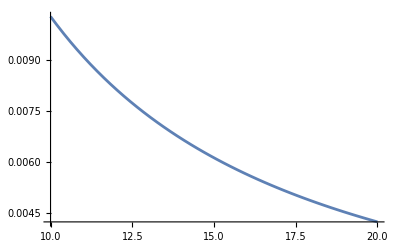

```mathematica
Plot[Hypergeometric1F1[1+C2/(2 √-En),2,2 √-En r]/.En->-3/.C2->1,{r,10, 20}]
Plot[HypergeometricU[1+C2/(2 √-En),2,2 √-En r]/.En->-3/.C2->1,{r,10, 20}]
```

```mathematica
FullSimplify[sol/.C[2] ->0,En<0&&C2>0]
```

{σ[r]→ⅇ^(-√-En r) r C[1] HypergeometricU[1+C2/(2 √-En),2,2 √-En r]}

```mathematica
Log[s0]==Log[c1/r Exp[-k r]]
```

Log[s0]==Log[(c1 ⅇ^(-k r))/r]

```mathematica
Log[(s0 r)/c1]/-r==k
```